```mathematica
ResourceFunction["MetamathImport"][URL["https://raw.githubusercontent.com/geohot/twitchcoq/master/metamath/twoplustwo.mm"],"ProofGraphStructure"]
```

-Graphics-

```mathematica
ResourceFunction["MetamathImport"][URL["https://raw.githubusercontent.com/geohot/twitchcoq/master/metamath/twoplustwo.mm"]]
```

<|Symbols→<||-→Constant[|-],wff→Constant[wff],term→Constant[term],var→Constant[var],s→Variable[s],t→Variable[t],u→Variable[u],s0→Variable[s0],s1→Variable[s1],t0→Variable[t0],t1→Variable[t1],v→Variable[v],x→Variable[x],y→Variable[y],z→Variable[z],0→Constant[0],S→Constant[S],+→Constant[+],*→Constant[*],BINOP→Constant[BINOP],binop→Variable[binop],not→Constant[not],or→Constant[or],and→Constant[and],implies→Constant[implies],iff→Constant[iff],LOGBINOP→Constant[LOGBINOP],logbinop→Variable[logbinop],=→Constant[=],<→Constant[<],BINPRED→Constant[BINPRED],binpred→Variable[binpred],forall→Constant[forall],exists→Constant[exists],QUANT→Constant[QUANT],quant→Variable[quant],phi→Variable[phi],psi→Variable[psi],chi→Variable[chi]|>,Statements→<|ts→Hypothesis[ts,{term,s}],tt→Hypothesis[tt,{term,t}],tu→Hypothesis[tu,{term,u}],ts0→Hypothesis[ts0,{term,s0}],ts1→Hypothesis[ts1,{term,s1}],tt0→Hypothesis[tt0,{term,t0}],tt1→Hypothesis[tt1,{term,t1}],varv→Hypothesis[varv,{var,v}],varx→Hypothesis[varx,{var,x}],vary→Hypothesis[vary,{var,y}],varz→Hypothesis[varz,{var,z}],binop_→Hypothesis[binop_,{BINOP,binop}],binop_plus→Axiom[binop_plus,{BINOP,+},{{},{},{}}],binop_times→Axiom[binop_times,{BINOP,*},{{},{},{}}],tvar→Axiom[tvar,{term,v},{{},{Hypothesis[varv,{var,v}]},{}}],tzero→Axiom[tzero,{term,0},{{},{},{}}],tsucc→Axiom[tsucc,{term,S,s},{{},{Hypothesis[ts,{term,s}]},{}}],tbinop→Axiom[tbinop,{term,binop,s,t},{{},{Hypothesis[ts,{term,s}],Hypothesis[tt,{term,t}],Hypothesis[binop_,{BINOP,binop}]},{}}],logbinop_→Hypothesis[logbinop_,{LOGBINOP,logbinop}],logbinopor→Axiom[logbinopor,{LOGBINOP,or},{{},{},{}}],logbinopand→Axiom[logbinopand,{LOGBINOP,and},{{},{},{}}],logbinopimplies→Axiom[logbinopimplies,{LOGBINOP,implies},{{},{},{}}],logbinopiff→Axiom[logbinopiff,{LOGBINOP,iff},{{},{},{}}],binpred_→Hypothesis[binpred_,{BINPRED,binpred}],binpred_equals→Axiom[binpred_equals,{BINPRED,=},{{},{},{}}],binpred_less_than→Axiom[binpred_less_than,{BINPRED,<},{{},{},{}}],quant_→Hypothesis[quant_,{QUANT,quant}],quant_all→Axiom[quant_all,{QUANT,forall},{{},{},{}}],quant_ex→Axiom[quant_ex,{QUANT,exists},{{},{},{}}],wff_phi→Hypothesis[wff_phi,{wff,phi}],wff_psi→Hypothesis[wff_psi,{wff,psi}],wff-chi→Hypothesis[wff-chi,{wff,chi}],wff_atom→Axiom[wff_atom,{wff,binpred,s,t},{{},{Hypothesis[ts,{term,s}],Hypothesis[tt,{term,t}],Hypothesis[binpred_,{BINPRED,binpred}]},{}}],wff_not→Axiom[wff_not,{wff,not,psi},{{},{Hypothesis[wff_psi,{wff,psi}]},{}}],wff_logbinop→Axiom[wff_logbinop,{wff,logbinop,psi,phi},{{},{Hypothesis[logbinop_,{LOGBINOP,logbinop}],Hypothesis[wff_phi,{wff,phi}],Hypothesis[wff_psi,{wff,psi}]},{}}],wff_quant→Axiom[wff_quant,{wff,quant,v,phi},{{},{Hypothesis[varv,{var,v}],Hypothesis[quant_,{QUANT,quant}],Hypothesis[wff_phi,{wff,phi}]},{}}],ax-1→Axiom[ax-1,{|-,implies,phi,implies,psi,phi},{{},{Hypothesis[wff_phi,{wff,phi}],Hypothesis[wff_psi,{wff,psi}]},{}}],ax-2→Axiom[ax-2,{|-,implies,implies,phi,implies,psi,chi,implies,implies,phi,psi,implies,phi,chi},{{},{Hypothesis[wff_phi,{wff,phi}],Hypothesis[wff_psi,{wff,psi}],Hypothesis[wff-chi,{wff,chi}]},{}}],ax-3→Axiom[ax-3,{|-,implies,implies,not,phi,not,psi,implies,psi,phi},{{},{Hypothesis[wff_phi,{wff,phi}],Hypothesis[wff_psi,{wff,psi}]},{}}],min→EssentialHypothesis[min,{|-,phi}],maj→EssentialHypothesis[maj,{|-,implies,phi,psi}],ax-mp→Axiom[ax-mp,{|-,psi},{{},{Hypothesis[wff_phi,{wff,phi}],Hypothesis[wff_psi,{wff,psi}]},{EssentialHypothesis[min,{|-,phi}],EssentialHypothesis[maj,{|-,implies,phi,psi}]}}],bi1→Axiom[bi1,{|-,implies,iff,phi,psi,implies,phi,psi},{{},{Hypothesis[wff_phi,{wff,phi}],Hypothesis[wff_psi,{wff,psi}]},{}}],bi2→Axiom[bi2,{|-,implies,iff,phi,psi,implies,psi,phi},{{},{Hypothesis[wff_phi,{wff,phi}],Hypothesis[wff_psi,{wff,psi}]},{}}],bi3→Axiom[bi3,{|-,implies,implies,phi,psi,implies,implies,psi,phi,iff,phi,psi},{{},{Hypothesis[wff_phi,{wff,phi}],Hypothesis[wff_psi,{wff,psi}]},{}}],df-an→Axiom[df-an,{|-,iff,and,phi,psi,not,implies,phi,not,psi},{{},{Hypothesis[wff_phi,{wff,phi}],Hypothesis[wff_psi,{wff,psi}]},{}}],df-or→Axiom[df-or,{|-,iff,or,phi,psi,implies,not,phi,psi},{{},{Hypothesis[wff_phi,{wff,phi}],Hypothesis[wff_psi,{wff,psi}]},{}}],eq-refl→Axiom[eq-refl,{|-,=,t,t},{{},{Hypothesis[tt,{term,t}]},{}}],eq-sym→Axiom[eq-sym,{|-,implies,=,s,t,=,t,s},{{},{Hypothesis[ts,{term,s}],Hypothesis[tt,{term,t}]},{}}],eq-trans→Axiom[eq-trans,{|-,implies,and,=,s,t,=,t,u,=,s,u},{{},{Hypothesis[ts,{term,s}],Hypothesis[tt,{term,t}],Hypothesis[tu,{term,u}]},{}}],eq-congr→Axiom[eq-congr,{|-,implies,and,=,s0,s1,=,t0,t1,iff,binpred,s0,t0,binpred,s1,t1},{{},{Hypothesis[ts0,{term,s0}],Hypothesis[ts1,{term,s1}],Hypothesis[tt0,{term,t0}],Hypothesis[tt1,{term,t1}],Hypothesis[binpred_,{BINPRED,binpred}]},{}}],eq-suc→Axiom[eq-suc,{|-,implies,=,s,t,=,S,s,S,t},{{},{Hypothesis[ts,{term,s}],Hypothesis[tt,{term,t}]},{}}],eq-binop→Axiom[eq-binop,{|-,implies,and,=,s0,s1,=,t0,t1,=,binop,s0,t0,binop,s1,t1},{{},{Hypothesis[ts0,{term,s0}],Hypothesis[ts1,{term,s1}],Hypothesis[tt0,{term,t0}],Hypothesis[tt1,{term,t1}],Hypothesis[binop_,{BINOP,binop}]},{}}],alpha_hyp1→EssentialHypothesis[alpha_hyp1,{|-,implies,phi,iff,psi,chi}],alpha_1→Axiom[alpha_1,{|-,implies,phi,iff,quant,x,psi,quant,x,chi},{{{phi,x}},{Hypothesis[varx,{var,x}],Hypothesis[quant_,{QUANT,quant}],Hypothesis[wff_phi,{wff,phi}],Hypothesis[wff_psi,{wff,psi}],Hypothesis[wff-chi,{wff,chi}]},{EssentialHypothesis[alpha_hyp1,{|-,implies,phi,iff,psi,chi}]}}],alpha_hyp2→EssentialHypothesis[alpha_hyp2,{|-,implies,phi,chi}],alpha_2→Axiom[alpha_2,{|-,implies,phi,forall,x,chi},{{{phi,x}},{Hypothesis[varx,{var,x}],Hypothesis[wff_phi,{wff,phi}],Hypothesis[wff-chi,{wff,chi}]},{EssentialHypothesis[alpha_hyp2,{|-,implies,phi,chi}]}}],alpha_3→Axiom[alpha_3,{|-,implies,forall,x,forall,y,implies,=,x,y,iff,phi,psi,iff,quant,x,phi,quant,y,psi},{{{phi,y},{psi,x},{x,y}},{Hypothesis[varx,{var,x}],Hypothesis[vary,{var,y}],Hypothesis[quant_,{QUANT,quant}],Hypothesis[wff_phi,{wff,phi}],Hypothesis[wff_psi,{wff,psi}]},{}}],all_elim→Axiom[all_elim,{|-,implies,forall,x,phi,forall,x,implies,=,x,t,phi},{{{t,x}},{Hypothesis[tt,{term,t}],Hypothesis[varx,{var,x}],Hypothesis[wff_phi,{wff,phi}]},{}}],all_elim_hyp2→EssentialHypothesis[all_elim_hyp2,{|-,implies,=,x,t,iff,phi,chi}],all_elim2→Axiom[all_elim2,{|-,implies,=,x,t,iff,quant,y,phi,quant,y,chi},{{{t,y},{x,y}},{Hypothesis[tt,{term,t}],Hypothesis[varx,{var,x}],Hypothesis[vary,{var,y}],Hypothesis[quant_,{QUANT,quant}],Hypothesis[wff_phi,{wff,phi}],Hypothesis[wff-chi,{wff,chi}]},{EssentialHypothesis[all_elim_hyp2,{|-,implies,=,x,t,iff,phi,chi}]}}],all_elim3_hyp1→EssentialHypothesis[all_elim3_hyp1,{|-,implies,=,x,t,iff,phi,chi}],all_elim3→Axiom[all_elim3,{|-,implies,forall,x,implies,=,x,t,phi,chi},{{{chi,x},{t,x}},{Hypothesis[tt,{term,t}],Hypothesis[varx,{var,x}],Hypothesis[wff_phi,{wff,phi}],Hypothesis[wff-chi,{wff,chi}]},{EssentialHypothesis[all_elim3_hyp1,{|-,implies,=,x,t,iff,phi,chi}]}}],exists_def→Axiom[exists_def,{|-,iff,exists,x,phi,not,forall,x,not,phi},{{},{Hypothesis[varx,{var,x}],Hypothesis[wff_phi,{wff,phi}]},{}}],pa_ax1→Axiom[pa_ax1,{|-,not,=,0,S,x},{{},{Hypothesis[varx,{var,x}]},{}}],pa_ax2→Axiom[pa_ax2,{|-,implies,=,S,x,S,y,=,x,y},{{},{Hypothesis[varx,{var,x}],Hypothesis[vary,{var,y}]},{}}],pa_ax3→Axiom[pa_ax3,{|-,=,x,+,x,0},{{},{Hypothesis[varx,{var,x}]},{}}],pa_ax4→Axiom[pa_ax4,{|-,=,S,+,x,y,+,x,S,y},{{},{Hypothesis[varx,{var,x}],Hypothesis[vary,{var,y}]},{}}],pa_ax5→Axiom[pa_ax5,{|-,=,0,*,x,0},{{},{Hypothesis[varx,{var,x}]},{}}],pa_ax6→Axiom[pa_ax6,{|-,=,+,*,x,y,x,*,x,S,y},{{},{Hypothesis[varx,{var,x}],Hypothesis[vary,{var,y}]},{}}],pa_ax7→Axiom[pa_ax7,{|-,iff,<,x,y,exists,z,=,y,+,x,S,z},{{},{Hypothesis[varx,{var,x}],Hypothesis[vary,{var,y}],Hypothesis[varz,{var,z}]},{}}],induction→Axiom[induction,{|-,implies,and,forall,y,implies,=,y,0,phi,forall,x,implies,forall,y,implies,=,y,x,phi,forall,y,implies,=,y,S,x,phi,forall,x,forall,y,implies,=,y,x,phi},{{{phi,x},{x,y}},{Hypothesis[varx,{var,x}],Hypothesis[vary,{var,y}],Hypothesis[wff_phi,{wff,phi}]},{}}],mpd.1→EssentialHypothesis[mpd.1,{|-,implies,phi,psi}],mpd.2→EssentialHypothesis[mpd.2,{|-,implies,phi,implies,psi,chi}],mpd→Theorem[mpd,{|-,implies,phi,chi},{{},{Hypothesis[wff_phi,{wff,phi}],Hypothesis[wff_psi,{wff,psi}],Hypothesis[wff-chi,{wff,chi}]},{EssentialHypothesis[mpd.1,{|-,implies,phi,psi}],EssentialHypothesis[mpd.2,{|-,implies,phi,implies,psi,chi}]}},{(,logbinopimplies,wff_logbinop,ax-2,ax-mp,),FBAGZFCAGZDFFCBGAGFKJGEABCHII}],syl.1→EssentialHypothesis[syl.1,{|-,implies,phi,psi}],syl.2→EssentialHypothesis[syl.2,{|-,implies,psi,chi}],syl→Theorem[syl,{|-,implies,phi,chi},{{},{Hypothesis[wff_phi,{wff,phi}],Hypothesis[wff_psi,{wff,psi}],Hypothesis[wff-chi,{wff,chi}]},{EssentialHypothesis[syl.1,{|-,implies,phi,psi}],EssentialHypothesis[syl.2,{|-,implies,psi,chi}]}},{(,logbinopimplies,wff_logbinop,ax-1,ax-mp,mpd,),ABCDFCBGZFKAGEKAHIJ}],id→Theorem[id,{|-,implies,phi,phi},{{},{Hypothesis[wff_phi,{wff,phi}]},{}},{(,logbinopimplies,wff_logbinop,ax-1,mpd,),ABAACZAAADAFDE}],absurd→Theorem[absurd,{|-,implies,not,phi,implies,phi,psi},{{},{Hypothesis[wff_phi,{wff,phi}],Hypothesis[wff_psi,{wff,psi}]},{}},{(,wff_not,logbinopimplies,wff_logbinop,ax-1,ax-3,syl,),ACZDIBCZEDBAEIJFBAGH}],com12.1→EssentialHypothesis[com12.1,{|-,implies,phi,implies,psi,chi}],com12→Theorem[com12,{|-,implies,psi,implies,phi,chi},{{},{Hypothesis[wff_phi,{wff,phi}],Hypothesis[wff_psi,{wff,psi}],Hypothesis[wff-chi,{wff,chi}]},{EssentialHypothesis[com12.1,{|-,implies,phi,implies,psi,chi}]}},{(,logbinopimplies,wff_logbinop,ax-1,ax-2,ax-mp,syl,),BEBAFZECAFZBAGEECBFAFE,LKFDABCHIJ}],imidm.1→EssentialHypothesis[imidm.1,{|-,implies,phi,implies,phi,psi}],imidm→Theorem[imidm,{|-,implies,phi,psi},{{},{Hypothesis[wff_phi,{wff,phi}],Hypothesis[wff_psi,{wff,psi}]},{EssentialHypothesis[imidm.1,{|-,implies,phi,implies,phi,psi}]}},{(,logbinopimplies,wff_logbinop,id,com12,mpd,),ADBAEZBCIABIFGH}],contra→Theorem[contra,{|-,implies,implies,not,phi,phi,phi},{{},{Hypothesis[wff_phi,{wff,phi}]},{}},{(,logbinopimplies,wff_not,wff_logbinop,absurd,ax-2,ax-mp,ax-3,syl,imidm,),BA,ACZDZALBLCZKDZBALDBBMADKDBNLDAMEKAMFGALHIJ}],notnot2→Theorem[notnot2,{|-,implies,not,not,phi,phi},{{},{Hypothesis[wff_phi,{wff,phi}]},{}},{(,wff_not,logbinopimplies,wff_logbinop,absurd,contra,syl,),ABZBCAHDAHAEAFG}],imim2→Theorem[imim2,{|-,implies,implies,psi,chi,implies,implies,phi,psi,implies,phi,chi},{{},{Hypothesis[wff_phi,{wff,phi}],Hypothesis[wff_psi,{wff,psi}],Hypothesis[wff-chi,{wff,chi}]},{}},{(,logbinopimplies,wff_logbinop,ax-1,ax-2,syl,),DCBEZDIAEDDCAEDBAEEIAFABCGH}],con2→Theorem[con2,{|-,implies,implies,phi,not,psi,implies,psi,not,phi},{{},{Hypothesis[wff_phi,{wff,phi}],Hypothesis[wff_psi,{wff,psi}]},{}},{(,logbinopimplies,wff_not,wff_logbinop,notnot2,imim2,com12,ax-mp,ax-3,syl,),CBDZAEZCLADZDZEZCNBECAOEZCPMEAFMQPOALGHINBJK}],notnot1→Theorem[notnot1,{|-,implies,phi,not,not,phi},{{},{Hypothesis[wff_phi,{wff,phi}]},{}},{(,logbinopimplies,wff_not,wff_logbinop,id,con2,ax-mp,),BACZHDBHCADHEHAFG}],con1i.1→EssentialHypothesis[con1i.1,{|-,implies,not,phi,psi}],con1i→Theorem[con1i,{|-,implies,not,psi,phi},{{},{Hypothesis[wff_phi,{wff,phi}],Hypothesis[wff_psi,{wff,psi}]},{EssentialHypothesis[con1i.1,{|-,implies,not,phi,psi}]}},{(,logbinopimplies,wff_not,wff_logbinop,notnot1,syl,ax-3,ax-mp,),DBEZEZAEZFD,AKFMBLCBGHAKIJ}],con3→Theorem[con3,{|-,implies,implies,phi,psi,implies,not,psi,not,phi},{{},{Hypothesis[wff_phi,{wff,phi}],Hypothesis[wff_psi,{wff,psi}]},{}},{(,logbinopimplies,wff_logbinop,wff_not,notnot1,imim2,ax-mp,con2,syl,),CBADZC,BEZEZADZCAELDCMBDCNKDBFABMGHALIJ}],andL→Theorem[andL,{|-,implies,and,phi,psi,phi},{{},{Hypothesis[wff_phi,{wff,phi}],Hypothesis[wff_psi,{wff,psi}]},{}},{(,logbinopand,wff_logbinop,logbinopimplies,logbinopiff,df-an,bi1,ax-mp,absurd,wff_not,con1i,syl,),CBADZEBKZADZKZAFQNDEQNDABGNQHIAPAOJLM}],andR→Theorem[andR,{|-,implies,and,phi,psi,psi},{{},{Hypothesis[wff_phi,{wff,phi}],Hypothesis[wff_psi,{wff,psi}]},{}},{(,logbinopand,wff_logbinop,logbinopimplies,wff_not,logbinopiff,df-an,bi1,ax-1,ax-mp,con1i,syl,),CBADZEBFZADZFZBGQNDEQNDABHNQIKBPOAJLM}],andI→Theorem[andI,{|-,implies,phi,implies,psi,and,phi,psi},{{},{Hypothesis[wff_phi,{wff,phi}],Hypothesis[wff_psi,{wff,psi}]},{}},{(,logbinopimplies,wff_not,wff_logbinop,logbinopand,com12,con2,syl,logbinopiff,id,df-an,bi2,ax-mp,imim2,),ACCBDZAEZDZBEZCFBAEZBEZACPQESQAPQKGQBH,ICTREZCUASEJRTEUBABLTRMNBRTONI}],andId.1→EssentialHypothesis[andId.1,{|-,implies,phi,psi}],andId.2→EssentialHypothesis[andId.2,{|-,implies,phi,chi}],andId→Theorem[andId,{|-,implies,phi,and,psi,chi},{{},{Hypothesis[wff_phi,{wff,phi}],Hypothesis[wff_psi,{wff,psi}],Hypothesis[wff-chi,{wff,chi}]},{EssentialHypothesis[andId.1,{|-,implies,phi,psi}],EssentialHypothesis[andId.2,{|-,implies,phi,chi}]}},{(,logbinopand,wff_logbinop,logbinopimplies,andI,syl,mpd,),ACFCBGZEABHLCGDBC,IJK}],imp.1→EssentialHypothesis[imp.1,{|-,implies,phi,implies,psi,chi}],imp→Theorem[imp,{|-,implies,and,phi,psi,chi},{{},{Hypothesis[wff_phi,{wff,phi}],Hypothesis[wff_psi,{wff,psi}],Hypothesis[wff-chi,{wff,chi}]},{EssentialHypothesis[imp.1,{|-,implies,phi,implies,psi,chi}]}},{(,logbinopand,wff_logbinop,andR,logbinopimplies,andL,syl,mpd,),EBAFZBCABGLA,HCBFABIDJK}],exp.1→EssentialHypothesis[exp.1,{|-,implies,and,phi,psi,chi}],exp→Theorem[exp,{|-,implies,phi,implies,psi,chi},{{},{Hypothesis[wff_phi,{wff,phi}],Hypothesis[wff_psi,{wff,psi}],Hypothesis[wff-chi,{wff,chi}]},{EssentialHypothesis[exp.1,{|-,implies,and,phi,psi,chi}]}},{(,logbinopimplies,logbinopand,wff_logbinop,andI,imim2,ax-mp,syl,),AEFBAGZBG,ZECBGZABHECLGENMGDBLCIJK}],wff_pa_ax1→Theorem[wff_pa_ax1,{wff,not,=,0,S,x},{{},{Hypothesis[varx,{var,x}]},{}},{tzero,varx,tvar,tsucc,binpred_equals,wff_atom,wff_not}],wff_pa_ax1_term→Theorem[wff_pa_ax1_term,{wff,not,=,0,S,t},{{},{Hypothesis[tt,{term,t}]},{}},{tzero,tt,tsucc,binpred_equals,wff_atom,wff_not}],int1→Theorem[int1,{|-,implies,chi,not,=,0,S,x},{{},{Hypothesis[varx,{var,x}],Hypothesis[wff-chi,{wff,chi}]},{}},{varx,wff_pa_ax1,logbinopimplies,varx,wff_pa_ax1,wff-chi,wff_logbinop,varx,pa_ax1,varx,wff_pa_ax1,wff-chi,ax-1,ax-mp}],int2→Theorem[int2,{|-,implies,psi,forall,x,not,=,0,S,x},{{{psi,x}},{Hypothesis[varx,{var,x}],Hypothesis[wff_psi,{wff,psi}]},{}},{varx,wff_psi,varx,wff_pa_ax1,varx,wff_psi,int1,alpha_2}],nocheat→Theorem[nocheat,{|-,forall,x,not,=,0,S,x},{{},{Hypothesis[varx,{var,x}]},{}},{vary,wff_pa_ax1,varx,quant_all,varx,wff_pa_ax1,wff_quant,vary,pa_ax1,varx,vary,wff_pa_ax1,int2,ax-mp}],nocheat2→Theorem[nocheat2,{|-,forall,x,implies,=,x,0,not,=,0,S,x},{{},{Hypothesis[varx,{var,x}]},{}},{varx,quant_all,varx,wff_pa_ax1,wff_quant,varx,quant_all,logbinopimplies,varx,wff_pa_ax1,varx,tvar,tzero,binpred_equals,wff_atom,wff_logbinop,wff_quant,varx,nocheat,tzero,varx,varx,wff_pa_ax1,all_elim,ax-mp}],nocheat2_wff→Theorem[nocheat2_wff,{wff,forall,x,implies,=,x,0,not,=,0,S,x},{{},{Hypothesis[varx,{var,x}]},{}},{varx,quant_all,logbinopimplies,varx,tvar,wff_pa_ax1_term,varx,tvar,tzero,binpred_equals,wff_atom,wff_logbinop,wff_quant}],tmp3→Theorem[tmp3,{|-,implies,and,=,t,t,=,x,0,iff,=,t,x,=,t,0},{{},{Hypothesis[tt,{term,t}],Hypothesis[varx,{var,x}]},{}},{tt,tt,varx,tvar,tzero,binpred_equals,eq-congr}],tmp3a→Theorem[tmp3a,{|-,implies,=,x,0,=,S,x,S,0},{{},{Hypothesis[varx,{var,x}]},{}},{varx,tvar,tzero,eq-suc}],tmp3b→Theorem[tmp3b,{|-,implies,and,=,0,0,=,S,x,S,0,iff,=,0,S,x,=,0,S,0},{{},{Hypothesis[varx,{var,x}]},{}},{tzero,tzero,varx,tvar,tsucc,tzero,tsucc,binpred_equals,eq-congr}],tmp3c→Theorem[tmp3c,{|-,implies,=,S,x,S,0,and,=,0,0,=,S,x,S,0},{{},{Hypothesis[varx,{var,x}]},{}},{(,tzero,binpred_equals,wff_atom,logbinopimplies,logbinopand,tvar,wff_logbinop,tsucc,eq-refl,andI,ax-mp,),BBCDZEFAGIBICDZMHNHBJMNKL}],eqeq2→Theorem[eqeq2,{|-,implies,=,s,t,iff,=,u,s,=,u,t},{{},{Hypothesis[ts,{term,s}],Hypothesis[tt,{term,t}],Hypothesis[tu,{term,u}]},{}},{(,binpred_equals,wff_atom,logbinopimplies,logbinopiff,logbinopand,andR,eq-sym,wff_logbinop,andL,syl,andId,eq-trans,exp,bi3,mpd,),ABDEZFCADEZCBDEZKZG,UATKZSUATHUASKZHBADEZUAKTUDUAUESUAIUDSUESUALABJMNCBAOMPSFUATKFUCUBKSTUAHTSKZH,STKUAUFTSSTISTLNCABOMPTUAQMR}],tmp3d→Theorem[tmp3d,{|-,implies,=,S,x,S,0,iff,=,0,S,x,=,0,S,0},{{},{Hypothesis[varx,{var,x}]},{}},{(,tvar,tsucc,tzero,eqeq2,),ABCDCDE}],tmp3e→Theorem[tmp3e,{|-,implies,=,x,0,iff,=,0,S,x,=,0,S,0},{{},{Hypothesis[varx,{var,x}]},{}},{(,tvar,tzero,binpred_equals,wff_atom,tsucc,logbinopiff,wff_logbinop,tmp3d,syl,eq-suc,),ABZCDELFZCFZDEGCNDECMDEHLCKAIJ}],notbi→Theorem[notbi,{|-,implies,iff,phi,psi,iff,not,phi,not,psi},{{},{Hypothesis[wff_phi,{wff,phi}],Hypothesis[wff_psi,{wff,psi}]},{}},{(,logbinopiff,wff_logbinop,logbinopimplies,wff_not,bi1,con3,syl,bi2,bi3,mpd,),CBADZEAFZBFZDZCONDZMEBADPABGABHIMEONDZEQPDMEABDRABJBAHINOKIL}],tmp3f→Theorem[tmp3f,{|-,implies,iff,=,0,S,x,=,0,S,0,iff,not,=,0,S,x,not,=,0,S,0},{{},{Hypothesis[varx,{var,x}]},{}},{(,tzero,tvar,tsucc,binpred_equals,wff_atom,notbi,),BACDEFBBDEFG}],cheat3→Theorem[cheat3,{|-,implies,=,x,0,iff,not,=,0,S,x,not,=,0,S,0},{{},{Hypothesis[varx,{var,x}]},{}},{(,tvar,tzero,binpred_equals,wff_atom,logbinopiff,tsucc,wff_logbinop,tmp3e,syl,wff_not,tmp3f,),ABZCDEFCCGDEZCMGDEZHFNKOKHAIALJ}],nocheat4→Theorem[nocheat4,{|-,implies,forall,x,implies,=,x,0,not,=,0,S,x,not,=,0,S,0},{{},{Hypothesis[varx,{var,x}]},{}},{tzero,varx,varx,tvar,wff_pa_ax1_term,tzero,wff_pa_ax1_term,varx,cheat3,all_elim3}],one_ne_zero→Theorem[one_ne_zero,{|-,not,=,0,S,0},{{},{},{}},{varx,nocheat2_wff,tzero,wff_pa_ax1_term,varx,nocheat2,varx,nocheat4,ax-mp}]|>|>

## Addition Facts

```mathematica
eq[succ[succ[0]],plus[succ[0],succ[0]]]
```

```mathematica
Table[eq[Nest[s,0,i+j],plus[Nest[s,0,i],Nest[s,0,j]]],{i,3},{j,3}]
```

{{eq[s[s[0]],plus[s[0],s[0]]],eq[s[s[s[0]]],plus[s[0],s[s[0]]]],eq[s[s[s[s[0]]]],plus[s[0],s[s[s[0]]]]]},{eq[s[s[s[0]]],plus[s[s[0]],s[0]]],eq[s[s[s[s[0]]]],plus[s[s[0]],s[s[0]]]],eq[s[s[s[s[s[0]]]]],plus[s[s[0]],s[s[s[0]]]]]},{eq[s[s[s[s[0]]]],plus[s[s[s[0]]],s[0]]],eq[s[s[s[s[s[0]]]]],plus[s[s[s[0]]],s[s[0]]]],eq[s[s[s[s[s[s[0]]]]]],plus[s[s[s[0]]],s[s[s[0]]]]]}}

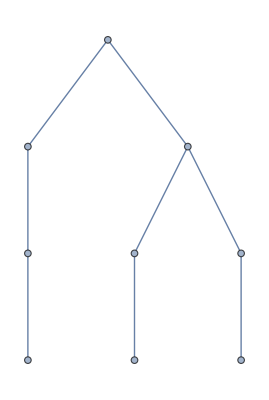
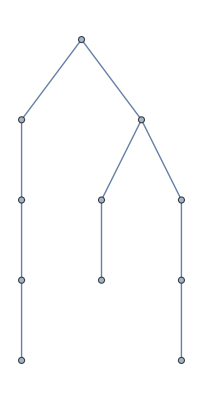
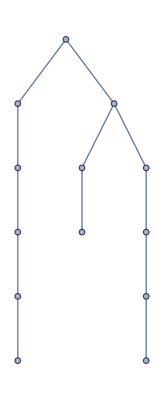
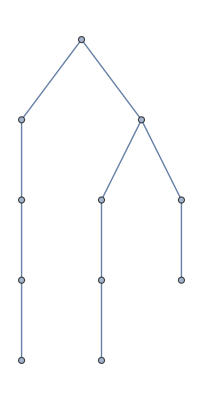
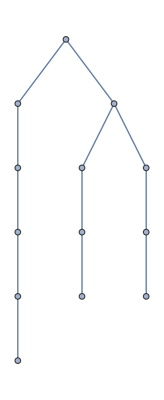
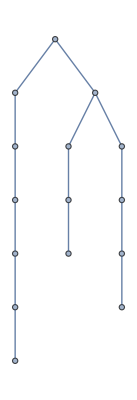
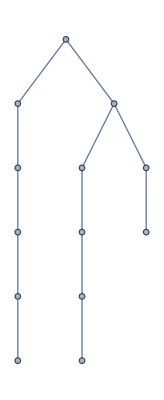
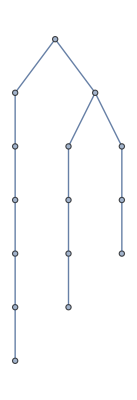

```mathematica
ExpressionGraph/@Flatten[%]
```

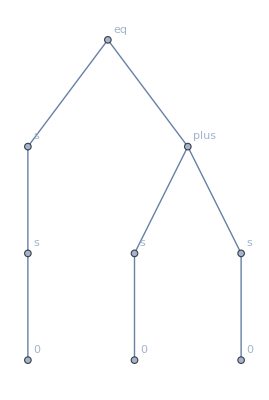
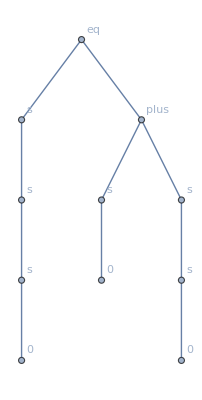
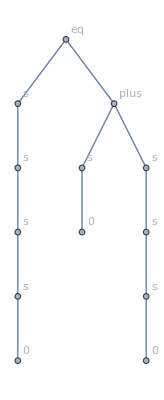
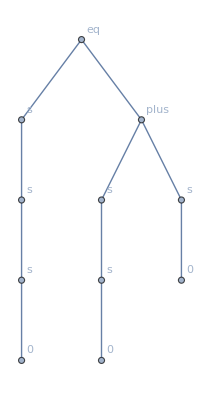
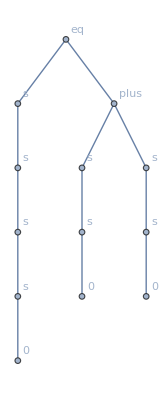
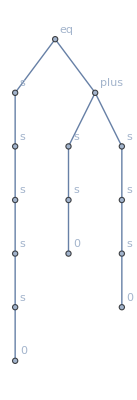
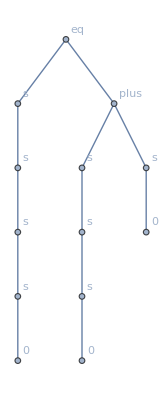
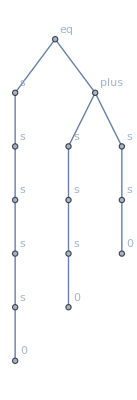

```mathematica
ExpressionGraph[#,VertexLabels->Automatic]&/@Flatten[%327]
```

```mathematica
VertexList[-Graphics-]
```

{1,2,3,4,5,6,7,8,9}

```mathematica
AnnotationValue[-Graphics-,VertexLabels]
```

{6→s,3→s,5→plus,8→s,7→0,4→0,9→0,2→s,1→eq}

```mathematica
EdgeList[-Graphics-]/.(AnnotationValue[-Graphics-,VertexLabels])
```

{eq<->s,s<->s,s<->0,eq<->plus,plus<->s,s<->0,plus<->s,s<->0}

```mathematica
atomify[g_]:=Graph[(DirectedEdge@@@EdgeList[g])/.(AnnotationValue[g,VertexLabels])]
```

```mathematica
ExpressionGraph[#,VertexLabels->Automatic]&/@Flatten[Table[eq[Nest[s,0,i+j],plus[Nest[s,0,i],Nest[s,0,j]]],{i,3},{j,3}]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
atomify/@%
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

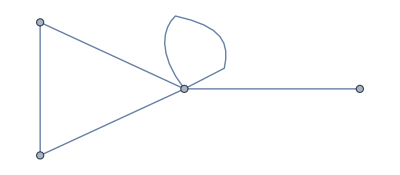

```mathematica
GraphUnion@@%
```

```mathematica
EdgeList/@%337
```

{{eq<->s,s<->s,s<->0,eq<->plus,plus<->s,s<->0,plus<->s,s<->0},{eq<->s,s<->s,s<->s,s<->0,eq<->plus,plus<->s,s<->0,plus<->s,s<->s,s<->0},{eq<->s,s<->s,s<->s,s<->s,s<->0,eq<->plus,plus<->s,s<->0,plus<->s,s<->s,s<->s,s<->0},{eq<->s,s<->s,s<->s,s<->0,eq<->plus,plus<->s,s<->s,s<->0,plus<->s,s<->0},{eq<->s,s<->s,s<->s,s<->s,s<->0,eq<->plus,plus<->s,s<->s,s<->0,plus<->s,s<->s,s<->0},{eq<->s,s<->s,s<->s,s<->s,s<->s,s<->0,eq<->plus,plus<->s,s<->s,s<->0,plus<->s,s<->s,s<->s,s<->0},{eq<->s,s<->s,s<->s,s<->s,s<->0,eq<->plus,plus<->s,s<->s,s<->s,s<->0,plus<->s,s<->0},{eq<->s,s<->s,s<->s,s<->s,s<->s,s<->0,eq<->plus,plus<->s,s<->s,s<->s,s<->0,plus<->s,s<->s,s<->0},{eq<->s,s<->s,s<->s,s<->s,s<->s,s<->s,s<->0,eq<->plus,plus<->s,s<->s,s<->s,s<->0,plus<->s,s<->s,s<->s,s<->0}}

```mathematica
Graph[Flatten[%]]
```

-Graphics-

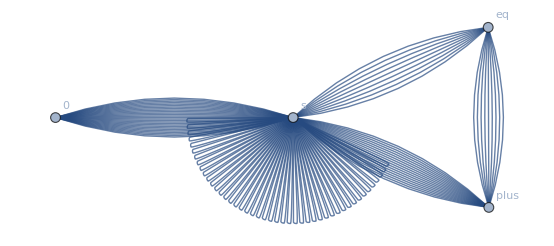

```mathematica
Graph[%,VertexLabels->Automatic]
```

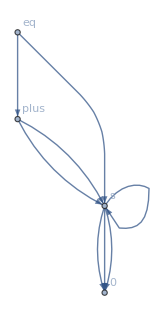

```mathematica
Graph[atomify[-Graphics-],VertexLabels->Automatic]
```

```mathematica
rootify[g_]:=Graph[Join[DirectedEdge@@@EdgeList[g],DirectedEdge@@@Reverse/@AnnotationValue[g,VertexLabels]],VertexLabels->(#->#&/@(Last/@AnnotationValue[g,VertexLabels]))]
```

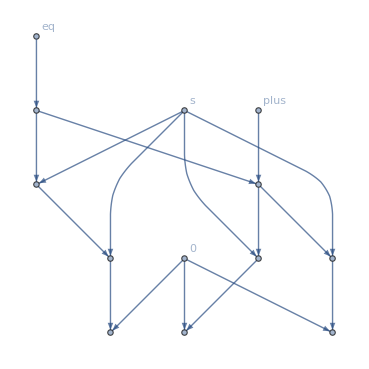

```mathematica
rootify[-Graphics-]
```

#### Really should use more of a WM approach with ordered relations

#### “Ultrapure mathematics”